```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
<<BISfit`;
<<Data`;
```

{31,8,3}

```mathematica
data=ColeData[];
Dimensions[data]
fdata=Map[Filterd,data];
Dimensions[fdata];
lfd=Map[Length,fdata]
(*filter fitted data*)
(*For[i=1,i≤Length[data*)
(*data//MatrixForm;*)

(* normalized data*)
ffdata=Flatten[fdata,1];
Dimensions[ffdata];
sdata=Standardize[ffdata];
nsdata=Reap[For[i=1;td=sdata,i≤Length[lfd],i++,
Sow[Take[td,lfd[[i]]]];
td=Drop[td,lfd[[i]]];
]][[2,1]];
```

{32,8,4}

{2,8,8,8,8,3,8,7,8,2,7,5,2,8,7,7,6,8,8,8,8,8,8,7,6,8,6,8,7,7,8,7}

```mathematica
Dimensions[nsdata]
lfd
```

{32}

{2,8,8,8,8,3,8,7,8,2,7,5,2,8,7,7,6,8,8,8,8,8,8,7,6,8,6,8,7,7,8,7}

```mathematica
fdata=nsdata;
```

```mathematica
(*data[[5,1,1]];
NumberQ[data[[5,1,1]]];
Dimensions[data[[5]]]
Abs[data[[5]]];
bl=Map[NumberQ,data[[5,2]]];*)
(*d=data[[5]];
td=d;

For[i=1,i≤Length[td],i,
(*delete ith element if not real*)
If[Length[Select[td[[i]],NumberQ[#]==False&]]>0,td=Drop[td,{i}];Continue[],i++];
];

t=StandardDeviation[td]
m=Mean[td]
For[i=1,i≤Length[td],i,
If[Length[Select[Abs[td[[i]]-m]-3t,#>0&]]≠0 ||Length[Select[td[[i]],#<0&]]≠0,td=Drop[td,{i}];Continue[],i++];
]
td
3t ;
td[[2]]-m-3t ;
Select[Abs[td[[2]]-m]-3t,#>0&];
(*Drop[data[[5]],2]*)
Length[Select[Map[NumberQ,data[[5,1]],{1}],#==False&]]*)
```

```mathematica
(*{mx1,mn1}={maxd,mind}/.{maxd->{200,120},mind->{65,10}}
td=fdata[[9]]
td[[2]]⟦1⟧>mx1[[1]]
For[i=1,i≤Length[td],i,
(*Another value boundary*)
If[td[[i]]⟦1⟧>mx1[[1]]||td[[i]][[2]]>mx1[[2]]||td[[i]]⟦1⟧<mn1[[1]]||td[[i]][[2]]<mn1[[2]],td=Drop[td,{i}];Continue[],i++];
];*)
```

```mathematica
Dimensions[fdata]
fdata[[2]]
```

{32}

{{-1.00115,-0.384765,2.27099,-0.328686},{-0.913978,-0.448444,1.86137,-0.228341},{-0.586862,-0.49706,1.0931,0.0307833},{-0.4609,-0.741522,0.281912,7.24381},{-0.986281,-0.410314,1.99688,-0.0952257},{-0.926634,-0.430242,1.73989,-0.203075},{-0.909736,-0.423001,1.72069,-0.19013},{-0.697485,-0.454308,1.2456,-0.300686}}

```mathematica
d1=Table[StandardDeviation[Flatten[fdata[[All,All,i]]]],{i,3}]
Mdistance[u_,v_]:=√(∑ _(i=1)^Length[u] ((u[[i]]-v[[i]])/d1[[i]])^2);
```

{14.0281,9.99842,0.0917497}

```mathematica
(*ddsf[d_]:=Module[
{},

Dimensions[Flatten[ds[[2,1]],1]]*)

ddiff=Flatten[Reap[For[i=1,i≤Length[fdata]-1,i++,
For[j=i+1,j≤Length[fdata],j++,
Sow[Flatten[Outer[EuclideanDistance,fdata[[i]],fdata[[j]],1]]]
]]
][[2,1]]];
dsame=Reap[For[i=1,i≤Length[fdata],i++,
For[j=1,j≤Length[fdata[[i]]]-1,j++,
For[k=j+1,k<=Length[fdata[[i]]],k++,
Sow[EuclideanDistance[fdata[[i]][[j]],fdata[[i]][[k]]]];
(*Sow[-Mdistance[fdata[[i]][[j]],fdata[[i]][[k]]]];*)
]]]
][[2,1]];
```

```mathematica
mdsame=Mean[dsame]
mddiff=Mean[ddiff]
ddsame=StandardDeviation[dsame]
dddiff=StandardDeviation[ddiff]
{ns,nd}={Length[dsame],Length[ddiff]}
Max[ddiff]
Max[dsame]
```

0.914776

2.54804

1.16382

1.29695

{677,22543}

11.1799

7.8561

```mathematica
(*find distance threshold for classify*)
```

```mathematica
dds=BinCounts[dsame,{0,12,0.15}]/ns;
ddd=BinCounts[ddiff,{0,12,0.15}]/nd;

(* now find it*)
For[i=1,i≤Length[ddd],i++,
If[dds[[i]]-ddd[[i]]≤0,Break[]];
]
i*0.15
i
```

1.2

8

```mathematica
(*now try classify*)
templ=fdata[[All,2]];
Length[templ];
```

```mathematica
classifyDist1[indata_,tmp_,th_]:=Module[
{group,i,j},
group=ConstantArray[ConstantArray[0,Length[tmp]],Length[indata]];
For[i=1,i≤Length[indata],i++,
For[j=1,j≤Length[tmp],j++,
If[EuclideanDistance[indata[[i]],tmp[[j]]]<th,
group[[i,j]]=1];
]];
group
]
group=classifyDist1[sdata,templ,1.2];
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,1,0,0,0},{1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1},{0,0,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,1,0,0,1},{0,0,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,1,0,0,1},{0,0,1,1,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,1,0,1,1,1,0,0,0,0,1,0,0,1},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,0,1},{0,0,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,0,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,0,1},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,1,0,1,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,1,1,0,0,0,0,0,1,0,0},{1,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,1,1,0,0,0,0,0,1,0,0},{1,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,1,1,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,1},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,1,0,0,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,1,0,1,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,1,0,1,0,0},{1,0,1,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,1,0,1,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,1,0,1,0,0},{1,0,1,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,1,0,1,0,0},{1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,1,0,1,0,0},{1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,1,1},{1,0,1,1,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,1,1,0,1,1,0,1,1,0,0},{1,0,1,1,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,1,1,0,1,1,0,1,1,0,0},{1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0},{1,0,1,1,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,1,1,0,1,1,0,1,1,0,0},{1,0,1,1,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,1,1,0,1,1,0,1,1,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,1,1,0,1,1,0,1,1,0,0},{1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,0},{1,0,1,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1,1,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,0},{1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,0,1,0,0},{1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,1,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,1,0,1,0,0,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,1,0,1,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,1,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,1,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,1,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,1,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,0,1,0,1,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,0,1,0,1,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,0,1,0,1,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,1,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,0,1,0,1,0},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,0,1,0,1,0},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,0,1,0,1,0},{1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0},{1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0},{1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0},{1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0},{1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0},{1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0},{1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(*true group is*)
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[sdata]];
For[i=1;k=1;n=1,i≤Length[lfd],i++,
For[m=1,m≤lfd[[i]],m++,
tg[[n,k]]=1;
n++;
];
k++;
]
```

```mathematica
(*check result*)
```

```mathematica
group;
```

```mathematica
VF[tg,group]
```

{0.138166,0.137993,0.143519}

```mathematica
{ftg,fg}={Flatten[tg],Flatten[group]};
err=HammingDistance[ftg,fg]/Length[fg]//N
```

0.138166

```mathematica
(* false positive*)
pt=Extract[fg,Position[ftg,0]];(*find the truth of the positive result*)
Far=Length[Select[pt,#==1&]]/Length[Select[ftg,#==0&]]//N

pf=Extract[fg,Position[ftg,1]];(*find the truth of the negative result*)
Frr=Length[Select[pf,#==0&]]/Length[Select[ftg,#==1&]]//N
```

0.137993

0.143519

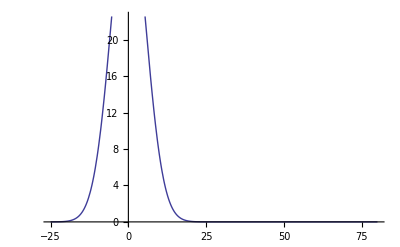

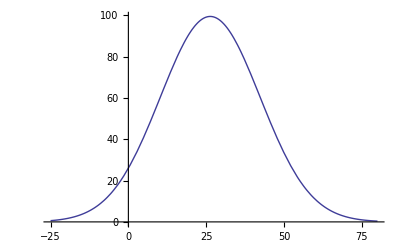

```mathematica
(*Ppdf1=Plot[500*PDF[NormalDistribution[mdsame,ddsame-7],x],{x,-25,80}]
Ppdf2=Plot[4000*PDF[NormalDistribution[mddiff,dddiff],x],{x,-25,80}]*)
```

```mathematica
(*sdsame=MovingAverage[dsame,{1,1,1}];
sddiff=MovingAverage[ddiff,{1,1,1}];*)
(*类概率密度*)
Pd=Length[ddiff]/(Length[dsame]+Length[ddiff]);
Ps=Length[dsame]/(Length[dsame]+Length[ddiff]);
```

```mathematica
h1=Histogram[Ps*sdsame,{0,10,0.1},ColorFunction->Function[{x},Black]]
(*BinCounts[Flatten[ds[[2,1]],1],1]*)
```

-Graphics-

```mathematica
(*Show[Ppdf1,h1,PlotRange->{{-5,25},{0,80}}]*)
```

-Graphics-

```mathematica
h2=Histogram[Pd*sddiff,{0,30,0.1}]
```

-Graphics-

```mathematica
(*Show[Ppdf2,h2,PlotRange->{{0,100},{0,100}}]*)
```

-Graphics-

```mathematica
Show[h2,h1,PlotRange->{{0,10},{0,80}}]
```

-Graphics-

307/2299

1992/2299

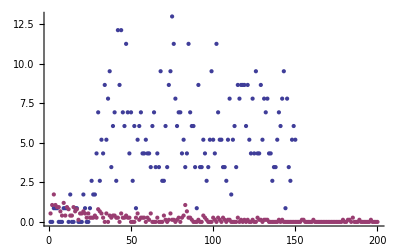

0.85

```mathematica
(*first *)
(*Pd=Length[ddiff]/(Length[dsame]+Length[ddiff]);
Ps=Length[dsame]/(Length[dsame]+Length[ddiff]);*)
(*find when his1=his2*)
bcdiff=Pd*BinCounts[ddiff,{0,15,0.1}];
bcsame=Ps*BinCounts[dsame,{0,20,0.1}];
Ps
Pd
ListPlot[{bcdiff,bcsame}]
l=Min[Length[bcdiff],Length[bcsame]];
dbc=bcsame[[1;;l]]-bcdiff[[1;;l]];
sdbc=MovingAverage[dbc,{1,1,1}];
t=1;k=1;
For[i=1,i≤l,i++,
If[sdbc[[i]]>0,t=i,
If[sdbc[[i]]<0,k=i;Break[],]
]
]
thd=(t+k)/2*0.1
```

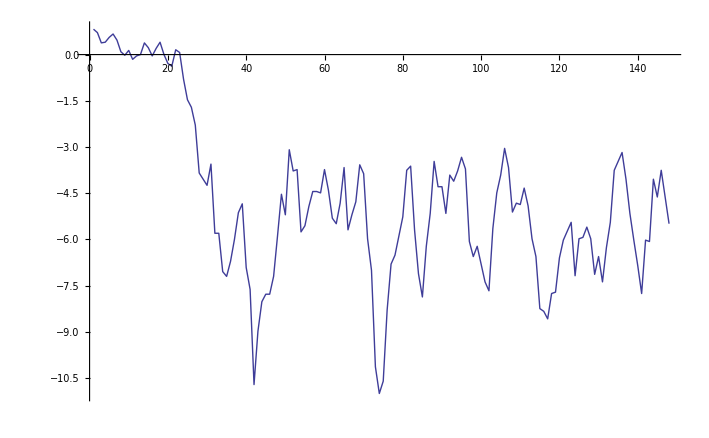

```mathematica
ListLinePlot[sdbc]
```

```mathematica
(*For[i=1,i≤Length[ddiff],i,
If[ddiff[i]>200000,ddiff=Delete[ddiff,i],i++]];*)
```

```mathematica
(*Position[ddiff,Select[ddiff,#>200000&]]
Length[tdd]*)
```

```mathematica
thd=9
ddiff2=Flatten[Reap[For[i=15,i≤30,i++,
For[j=i+1,j≤31,j++,
Sow[Flatten[Outer[EuclideanDistance,fdata[[i]],fdata[[j]],1]]]
]]
][[2,1]]];
dsame2=Reap[For[i=15,i≤31,i++,
For[j=1,j≤Length[fdata[[i]]]-1,j++,
For[k=j+1,k<=Length[fdata[[i]]],k++,
Sow[EuclideanDistance[fdata[[i]][[j]],fdata[[i]][[k]]]];
(*Sow[-EuclideanDistance[fdata[[i]][[j]],fdata[[i]][[k]]]];*)
]
]
]
][[2,1]];
(*using threshold*)
N[Length[Select[ddiff2,#≥thd&]]/Length[ddiff2]]
N[Length[Select[dsame2,#≤(thd)&]]/Length[dsame2]]
```

9

0.740959

0.882641

```mathematica
(*using EER*)
err1=Plot[Length[Select[ddiff,#<(x)&]]/Length[ddiff],{x,0,100}];
err2=Plot[Length[Select[dsame,#>x&]]/Length[dsame],{x,0,100}];
```

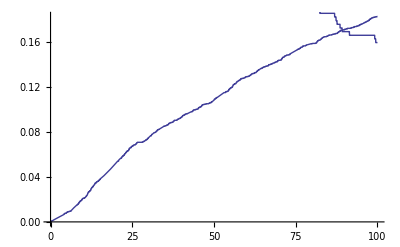

```mathematica
Show[err1,err2]
```

```mathematica
For[k=0.1,k<500,k=k+1,
If[Abs[Length[Select[ddiff,#≥(k)&]]/Length[ddiff]-
Length[Select[dsame,#≤(k)&]]/Length[dsame]]<0.05,Print[k];Break[];]
]
N[Length[Select[dsame,#≤(k)&]]/Length[dsame]]
N[Length[Select[ddiff2,#≥(k)&]]/Length[ddiff2]]
N[Length[Select[dsame2,#≤(k)&]]/Length[dsame2]]
```

9.1

0.814332

0.733726

0.882641

```mathematica
thd+k
```

20.35

```mathematica
(*try Parzen*)
```